```mathematica
(* uncomment if you need to install it

ResourceFunction["MaTeXInstall"][]
*)
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.9,<>]

computer-depending command

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2022\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs9.56.1\\bin\\gswin64c.exe"]
```

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2021\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.00.0\\bin\\gswin64c.exe"]
```

ConfigureMaTeX[pdfLaTeX→C:\texlive\2021\bin\win32\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.00.0\bin\gswin64c.exe]

```mathematica
<<MaTeX`
```

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

FileExistsQ::badfile: The specified argument  should be a valid string or File.

```mathematica
<<MaTeX`
```

Get::noopen: Cannot open MaTeX`.

$Failed

HatchFilling is a command for v13

```mathematica
plot=RegionPlot[{(2x y+3x+3y)(2x y -x-y)>=0,-4 x^2-4 y^2-2x y+3x+3y>=0},{x,-2,2},{y,-2,2},AspectRatio->1,PlotStyle->{{HatchFilling[1],Blue},{HatchFilling[0],Orange}},BaseStyle->{FontFamily->"Times",FontSize->20},PlotRangePadding->0,Frame->True,
FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX[" \\eta",Magnification->2],MaTeX["\\xi",Magnification->2]}];
```

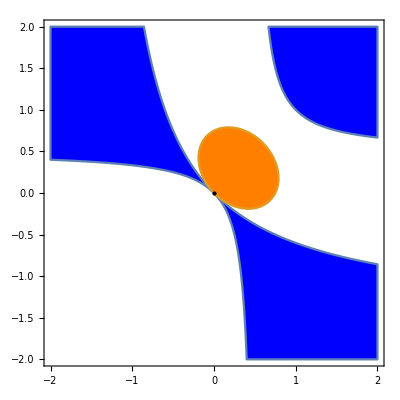

```mathematica
Show[plot,Graphics[{PointSize[Large],Point[{0,0}]}]]
```

```mathematica
Manipulate[ContourPlot[{1-√((b+d)(b+d))==√((2-b-b-d-e)(a+e-1)),1-√((b+e)(b+e))==√((2-b-b-d-e)(a+d-1)),d==1-b,e==1-b},{e,0,3},{d,0,3},PlotPoints->55,AspectRatio->1,ContourStyle->{{Dashed,Blue},{Dotted,Red},{AbsoluteDashing[{1,0}],Black},{AbsoluteDashing[{1,0}],Black}},BaseStyle->{FontFamily->"Times",FontSize->20},PlotRangePadding->0,Frame->True,FrameTicksStyle->Directive[Black,Thick],FrameLabel->{MaTeX[" \\eta",Magnification->2],MaTeX["\\xi",Magnification->2]},Epilog->{
Text[MaTeX["a=0.8",Magnification->2],{2,2}],Text[MaTeX["b=0.1",Magnification->2],{2,1.7}]}],{{a,.8},0,3,0.1},{{b,.1},0,1,0.1}]
```

In the following picture the line are ad hoc, therefore they holds only for only one specific choice of parameters.

```mathematica
Manipulate[RegionPlot[{
(√((b+d0)(c+d0))-1)^2<=(a+e0-1)(a+3-a-b-c-e0-d0-1),
(√((b+e0)(c+e0))-1)^2<=(a+d0-1)(a+3-a-b-c-e0-d0-1),
(√((b+3-a-b-c-e0-d0)(c+3-a-b-c-e0-d0))-1)^2<=(a+d0-1)(a+e0-1),
d0>=1-a&&e0>=1-a&&e0<=(2-b-c)-d0,
(-3+2 a-b-c)^2+(b-c)^2+(a-b) (3-a+2 b-c)+(a-c) (3-a-b+2 c)-√(-((a-b) (3-a+2 b-c)+(a-c) (3-a-b+2 c))^2+((-3+2 a-b-c)^2+(b-c)^2+(a-b) (3-a+2 b-c)+(a-c) (3-a-b+2 c))^2)-(3-a-b-c-d0-2 e0)^2-(d0-e0)^2-(-3+a+b+c+2 d0+e0)^2>=0
},{e0,-1.5,1.5},{d0,-1.5,1.5},PlotPoints->100,
PlotStyle->{{HatchFilling[0,8,1],Red},{HatchFilling[-1,8,1],Green},{HatchFilling[1,8,1],Blue},{Gray,Opacity[.5]},{Black,Opacity[.5]}},
BoundaryStyle->{1->Directive[Red,Thick],2->Directive[Green,Thick],3->Directive[Blue,Thick],4->Directive[Gray,Opacity[.1]],5->Directive[Black,Thick]},Frame->None,Epilog->{ Arrow[{{-1.6,0},{1.5,0}}],Arrow[{{0,-1.6},{0,1.5}}],
Arrow[{{0.7,.7},{.45,.4}}],
Text[MaTeX["d",Magnification->1],{-.15,1.47}],
Text[MaTeX["e",Magnification->1],{1.47,-.15}],
Line[{{-1,2},{2,-1}}],Line[{{-1.5,.1},{1.5,.1}}],Line[{{.1,1.5},{.1,-1.5}}],
Text[MaTeX["d=1-a",Magnification->1],{1.3,.15}],
Text[MaTeX["e=1-a",Magnification->1],{.35,-.35}],
Rotate[Text[MaTeX["d=2-b-c-e",Magnification->1],{-.35,1.25}],-π/4],
Text[MaTeX["\mbox{hessian}",Magnification->1],{.74,.74}]}],{{a,.9},.1,1.5,.1},{{b,0.9},0,1.5,.1},{{c,0.1},0,1.5,.1}]
```

```mathematica
RegionPlot[
{(-1+√((0.1+d0) (0.9+d0)))^2<=(1.-d0-e0) (-0.1+e0),(-1+√((0.1+e0) (0.9+e0)))^2<=(-0.1+d0) (1.-d0-e0),(-1+√((1.2-d0-e0) (2-d0-e0)))^2<=(-0.1+d0) (-0.1+e0),
d0>=.1&&e0>=.1&&e0<=1-d0,
0.096-(1.1-d0-2 e0)^2-(d0-e0)^2-(-1.1+2 d0+e0)^2>=0
},{e0,-1.5,1.5},{d0,-1.5,1.5},PlotPoints->100,
PlotStyle->{{HatchFilling[0,2,4],Red},{HatchFilling[-1,2,4],Green},{HatchFilling[1,2,4],Blue},{Gray,Opacity[.5]},{Black,Opacity[.5]}},
BoundaryStyle->{1->Directive[Red,Thick],2->Directive[Green,Thick],3->Directive[Blue,Thick],4->Directive[Gray,Opacity[.1]],5->Directive[Black,Thick]},Frame->None,Epilog->{ Arrow[{{-1.6,0},{1.5,0}}],Arrow[{{0,-1.6},{0,1.5}}],
Arrow[{{0.7,.7},{.45,.4}}],
Text[MaTeX["d",Magnification->1],{-.1,1.45}],
Text[MaTeX["e",Magnification->1],{1.44,-.14}],
Line[{{-1,2},{2,-1}}],Line[{{-1.5,.1},{1.5,.1}}],Line[{{.1,1.5},{.1,-1.5}}],
Text[MaTeX["d=1-a",Magnification->1],{1.2,.15}],
Text[MaTeX["e=1-a",Magnification->1],{.35,-.35}],
Rotate[Text[MaTeX["d=2-b-c-e",Magnification->1],{-.35,1.24}],-π/4],
Text[MaTeX["\mbox{hessian}",Magnification->1],{.74,.74}]}]
```

-Graphics-